when doing a lot of maths, we need someone way to be absolutely sure that no mistake has been made . One way is just to reduce things several times, and through different routes . I think you must have done that, as I' ve never found any mistakes . I personally tend to deduce things on paper, then check them in Mathematica. I’ll show you how I do this below.

```mathematica
Below I check equation (29) which relates the potentials to the stress
```

```mathematica
ClearAll[subBessel];

(*the stress from the strain*)
σfun[ϵ_]:= λ Tr[ϵ] IdentityMatrix[3] + 2 μ ϵ

(*the stain from the displacement vector*)
ϵfun[u_] :=Module[{ϵ1 = Grad[u,{r,θ,z},"Cylindrical"]},
Return[ϵ1/2+ϵ1ᵀ/2]
]

(*the displacement vector from the potentials*)
ufun[ϕ_,ψ_] := Grad[ϕ,{r,θ,z},"Cylindrical"]+ 
Curl[{0,0,ψ},{r,θ,z},"Cylindrical"]

(*Some quick checks*)

(* Checked: this is the same as the displacement equation in the report*)
ufun[ϕ[r,θ],ψ[r,θ]]//MatrixForm

(* Checked: this is the same as the strain equation in the report*)
ϵfun[{ur[r,θ],uθ[r,θ],0}]//MatrixForm;

(* Checked: this is the same as the first equation in the report that gives the stress in terms of the displacement*)
σfun[ϵfun[{ur[r,θ],uθ[r,θ],0}]][[1;;2,1]]//Simplify

σfun[ϵfun[ufun[ϕ[r,θ],ψ[r,θ]]]][[1;;2,1]]//Simplify;
```

((ψ^(0,1)[r,θ])/r+ϕ^(1,0)[r,θ]
(ϕ^(0,1)[r,θ])/r-ψ^(1,0)[r,θ]
0)

{(λ ur[r,θ]+λ uθ^(0,1)[r,θ]+r (λ+2 μ) ur^(1,0)[r,θ])/r,(μ (-uθ[r,θ]+ur^(0,1)[r,θ]+r uθ^(1,0)[r,θ]))/r}

```mathematica
(*The equation relating the potentials to the stress in the report was*)
(*Σ[ϕ_,ψ_]:= ρ { (2 cS^2 kP^2 -  ω^2  )ϕ +  2 cS^2 D[ϕ,{r,2}] +  2 cS^2 D[1/r D[ψ,θ],r],2 cS^2 D[1/r D[ϕ,θ],r] - ω^2 ψ -2 cS^2 D[ψ,{r,2}]}*)
(*Note the simplification ω^2-> cS^2 kS^2*)
Σ[ϕ_,ψ_]:= ρ cS^2{ (2 kP^2 -   kS^2)ϕ +  2  D[ϕ,{r,2}] +  2 D[1/r D[ψ,θ],r],2 D[1/r D[ϕ,θ],r] -  kS^2 ψ -2D[ψ,{r,2}]}

(*Let's check if they are the same*)
$Assumptions={r2>0,r1>0,r>0,0<θ<2π};

subBessel[m_] = {BesselJ[m,kr_] :> kr/(2 m) (BesselJ[m-1,kr] + BesselJ[m+1,kr] ) };


Nϕ= BesselJ[n, r kP] ⅇ^(ⅈ n θ)/.n->-4;
Nψ= BesselJ[n, r kS] ⅇ^(ⅈ n θ)/.n->1;
σ2 =(σfun@ϵfun@ufun[Nϕ ,Nψ])[[1]][[1;;2]];
σ2-Σ[Nϕ,Nψ]//.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}/.{cS -> ω/kS,cP -> ω/kP} //FullSimplify
```

{0,0}

### Extract the stress and displacement on some boundary for one mode

```mathematica
ClearAll[n]
submodes = {ϕ -> a[n]BesselJ[n,kP r] ⅇ^(ⅈ n θ) + b[n]HankelH1[n,kP r] ⅇ^(ⅈ n θ),ψ -> c[n]BesselJ[n,kS r] ⅇ^(ⅈ n θ) + d[n]HankelH1[n,kS r] ⅇ^(ⅈ n θ)};

 Σmodes= Σ[ϕ/.submodes,ψ/.submodes];
umodes= ufun[ϕ/.submodes,ψ/.submodes][[1;;2]];

coes = {a[n],b[n],c[n],d[n]};
Σn =Coefficient[Σmodes,#]&/@coes;
Σn = Σnᵀ //Simplify;

un =Coefficient[umodes,#]&/@coes;
un = unᵀ //Simplify;

(*A quick check*)
Σn.coes == Σmodes//Simplify
un.coes == umodes//Simplify

(*Pressure potential modes*)
Σn[[All,1]] //MatrixForm//Simplify
un[[All,1]]  //MatrixForm//Simplify

(*Shear potential modes*)
Σn[[All,3]] //MatrixForm//Simplify
un[[All,3]]  //MatrixForm//Simplify
```

True

True

(-(cS^2 ⅇ^(ⅈ n θ) ρ (2 kP r BesselJ[-1+n,kP r]+(-2 n-2 n^2+kS^2 r^2) BesselJ[n,kP r]))/r^2
(ⅈ cS^2 ⅇ^(ⅈ n θ) n ρ (kP r BesselJ[-1+n,kP r]-2 BesselJ[n,kP r]-kP r BesselJ[1+n,kP r]))/r^2)

(1/2 ⅇ^(ⅈ n θ) kP (BesselJ[-1+n,kP r]-BesselJ[1+n,kP r])
(ⅈ ⅇ^(ⅈ n θ) n BesselJ[n,kP r])/r)

((ⅈ cS^2 ⅇ^(ⅈ n θ) n ρ (kS r BesselJ[-1+n,kS r]-2 BesselJ[n,kS r]-kS r BesselJ[1+n,kS r]))/r^2
(cS^2 ⅇ^(ⅈ n θ) ρ (2 kS r BesselJ[-1+n,kS r]+(-2 n-2 n^2+kS^2 r^2) BesselJ[n,kS r]))/r^2)

((ⅈ ⅇ^(ⅈ n θ) n BesselJ[n,kS r])/r
-1/2 ⅇ^(ⅈ n θ) kS (BesselJ[-1+n,kS r]-BesselJ[1+n,kS r]))

```mathematica
Σn2 = Σn/ⅇ^(ⅈ n θ) /.{ ρ -> (r^2 ρS)/cS^2, BesselJ[n_,a_]:> Subscript[J, n][a], HankelH1[n_,a_]:> Subscript[H, n][a]} //Simplify;

un2 = un/ⅇ^(ⅈ n θ) /.{  BesselJ[n_,a_]:> Subscript[J, n][a], HankelH1[n_,a_]:> Subscript[H, n][a]} //Simplify;
```

```mathematica
(*Extract only the 1st and 3rd column of the stress mode*)
Vs =Transpose[Σn2][[{1,3}]];

(*A quick check that swapping J for H turns the 1st column into 2nd, and the 3rd column into the 4th*)
Transpose[{Vs[[1]],Vs[[1]]/.J->H,Vs[[2]],Vs[[2]]/.J->H}] == Σn2 //Simplify
Vs[[1]]/.{Subscript[J, n_][a_] :> J[n,a]}
Vs[[2]]/.{Subscript[J, n_][a_] :> J[n,a]}

(*Extract only the 1st and 3rd column of the displacement mode*)
Vs =Transpose[un2][[{1,3}]];

(*A quick check that swapping J for H turns the 1st column into 2nd, and the 3rd column into the 4th*)
Transpose[{Vs[[1]],Vs[[1]]/.J->H,Vs[[2]],Vs[[2]]/.J->H}] == un2 //Simplify
Vs[[1]]/.{Subscript[J, n_][a_] :> J[n,a]}
Vs[[2]]/.{Subscript[J, n_][a_] :> J[n,a]}
```

True

{-ρS (2 kP r J[-1+n,kP r]+(-2 n-2 n^2+kS^2 r^2) J[n,kP r]),ⅈ n ρS (kP r J[-1+n,kP r]-2 J[n,kP r]-kP r J[1+n,kP r])}

{ⅈ n ρS (kS r J[-1+n,kS r]-2 J[n,kS r]-kS r J[1+n,kS r]),ρS (2 kS r J[-1+n,kS r]+(-2 n-2 n^2+kS^2 r^2) J[n,kS r])}

True

{1/2 kP (J[-1+n,kP r]-J[1+n,kP r]),(ⅈ n J[n,kP r])/r}

{(ⅈ n J[n,kS r])/r,-1/2 kS (J[-1+n,kS r]-J[1+n,kS r])}

```mathematica
Formulate the matrix M and do some numerical checks;
(* The simplest direct problem: specify the forcing everywhere on an inner and outer radius*)
(* This allows for a Fourier type solution shown below*)

eqs =(Σmodes/.r-> r1)~Join~(Σmodes/.r->r2);
coes = {a[n],b[n],c[n],d[n]};
M =Coefficient[eqs/ⅇ^(ⅈ n θ) ,#]&/@coes;
M = Mᵀ //Simplify;
(*A quick check*)
M.coes == eqs/ⅇ^(ⅈ n θ)  //Simplify

M;
```

True

```mathematica
(*Numerical check of stability*)
(*Even with condition number 10^8 we can still get solutions with accuracy around 10^-8, this is because Float64, the most common floating number has a precision of 10^-16*)
subN = {cS -> 1.0, cP -> 2.0,r1 -> 0.5,r2 -> 1.0,ρ-> 1.0};
NM = M/.{θ->0 ,kP -> ω/cP,kS -> ω/cS}//.subN;

n0 = 6;ω0 = 5.1;
Nb = RandomReal[4,4];
Ncoes = LinearSolve[NM/.{n->n0,ω ->ω0 },Nb];
Norm[NM.Ncoes - Nb/.{n->n0,ω ->ω0 }] / Norm[Nb]
```

6.51473×10^-15

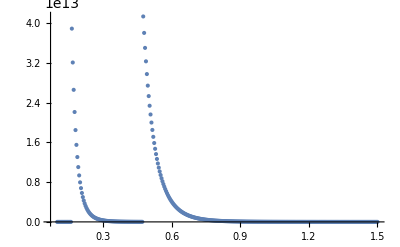

```mathematica
(*A bit of a strange pattern, am not sure why*)
CondNum[A_]:=  (
sv = SingularValueList[A/.{n->n0,ω ->ω0 }];
sv[[1]]/Last@sv
)
ωs=Range[0.1,1.5,0.004];
CondNum[NM/.{n->4,ω -># }]&/@ωs;
ListPlot[Transpose[{ωs,%}],PlotRange->All]

(*I'm guessing the peaks are the resonant frequencies?*)
```

### Checking if using HankelH1 and HankelH2 would improve conditioning

```mathematica
CondNum[A_]:=  (
sv = SingularValueList[A];
sv[[1]]/Last@sv
);
no = 8;
subN = {ρ->2.0,cS -> 2.0, cP -> 3.0, ω -> 8.5,r1->4.5,r2->5.0};
subN = subN~Join~({kP-> ω / cP,kS-> ω / cS}/.subN)

JMN=M/.subN;
H2MN=M/.BesselJ-> HankelH2/.subN;

H2MN/.n->no//CondNum
JMN/.n->no//CondNum
```

```mathematica
subN = {ρ->2.0,cS -> 2.0, cP -> 3.0, r1->4.5,r2->5.0};
subN = subN~Join~({kP-> ω / cP,kS-> ω / cS}/.subN);

no = 1;
H2MN=M/.BesselJ-> HankelH2/.subN/.n->no;
Normal[Series[H2MN,{ω,0,3}]]-Normal[Series[H2MN,{ω,0,2}]]//Chop//MatrixForm
```

((0.+0.742723 ⅈ) ω^3 ((-0.139038+1.5708 ⅈ)+1. Log[ω]) | (0.-0.742723 ⅈ) ω^3 ((-0.139038-1.5708 ⅈ)+1. Log[ω]) | -0.716197 ω^3 ((-0.0550013+1.5708 ⅈ)+1. Log[ω]) | 0.716197 ω^3 ((-0.0550013-1.5708 ⅈ)+1. Log[ω])
-0.212207 ω^3 ((-0.460466+1.5708 ⅈ)+1. Log[ω]) | 0.212207 ω^3 ((-0.460466-1.5708 ⅈ)+1. Log[ω]) | (0.-0.716197 ⅈ) ω^3 ((0.444999+1.5708 ⅈ)+1. Log[ω]) | 0.716197 ω^3 ((1.5708+0.444999 ⅈ)+(0.+1. ⅈ) Log[ω])
(0.+0.825248 ⅈ) ω^3 ((-0.0336773+1.5708 ⅈ)+1. Log[ω]) | (0.-0.825248 ⅈ) ω^3 ((-0.0336773-1.5708 ⅈ)+1. Log[ω]) | -0.795775 ω^3 ((0.0503592+1.5708 ⅈ)+1. Log[ω]) | 0.795775 ω^3 ((0.0503592-1.5708 ⅈ)+1. Log[ω])
-0.235785 ω^3 ((-0.355106+1.5708 ⅈ)+1. Log[ω]) | 0.235785 ω^3 ((-0.355106-1.5708 ⅈ)+1. Log[ω]) | (0.-0.795775 ⅈ) ω^3 ((0.550359+1.5708 ⅈ)+1. Log[ω]) | 0.795775 ω^3 ((1.5708+0.550359 ⅈ)+(0.+1. ⅈ) Log[ω]))

```mathematica
Series[M/.n->1/.{kP-> ω / cP,kS-> ω / cS},{ω,0,2}]//Normal//MatrixForm
```

```mathematica
Series[M/.BesselJ-> HankelH2/.n->1/.{kP-> ω / cP,kS-> ω / cS},{ω,0,0}]//Normal//MatrixForm
```

((8 ⅈ cP cS^2 ρ)/(π r1^3 ω) | -(8 ⅈ cP cS^2 ρ)/(π r1^3 ω) | (8 cS^3 ρ)/(π r1^3 ω) | -(8 cS^3 ρ)/(π r1^3 ω)
(8 cP cS^2 ρ)/(π r1^3 ω) | -(8 cP cS^2 ρ)/(π r1^3 ω) | -(8 ⅈ cS^3 ρ)/(π r1^3 ω) | (8 ⅈ cS^3 ρ)/(π r1^3 ω)
(8 ⅈ cP cS^2 ρ)/(π r2^3 ω) | -(8 ⅈ cP cS^2 ρ)/(π r2^3 ω) | (8 cS^3 ρ)/(π r2^3 ω) | -(8 cS^3 ρ)/(π r2^3 ω)
(8 cP cS^2 ρ)/(π r2^3 ω) | -(8 cP cS^2 ρ)/(π r2^3 ω) | -(8 ⅈ cS^3 ρ)/(π r2^3 ω) | (8 ⅈ cS^3 ρ)/(π r2^3 ω))

```mathematica
SingularValueList[JMN/.n->3]
```

{4.21651×10^19,2.36723×10^10}

3.46943×10^9

```mathematica
The principal of virtual work
```

```mathematica
(*first just check local balance of momentum from one mode*)
ClearAll[n]
Laplacian[ϕ/.submodes,{r,θ,z},"Cylindrical"]+kP^2(ϕ/.submodes)//FullSimplify
```

0

```mathematica
displace = ufun[ϕ/.submodes,ψ/.submodes];
stress =(σfun@ϵfun@ufun[ϕ/.submodes,ψ/.submodes]);
Divstress= Div[stress,{r,θ,z},"Cylindrical"] ;

ω^2 ρ umodes+Divstress[[1;;2]]//.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}/.{cS -> ω/kS,cP -> ω/kP} //FullSimplify
-Divstress +(λ+μ)Grad[Div[displace,{r,θ,z},"Cylindrical"],{r,θ,z},"Cylindrical"] + μ Laplacian[displace,{r,θ,z},"Cylindrical"] //.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}//.{cS -> ω/kS,cP -> ω/kP} //FullSimplify
```

```mathematica
{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}/.{cS -> ω/kS,cP -> ω/kP}
```

```mathematica
{μ->(ρ ω^2)/kS^2,λ->-2 (ρ ω^2)/kS^2+(ρ ω^2)/kP^2}
```

```mathematica
(*For the virtual displacement, or test function, we use*)
W = {w[1],w[2],w[3]}BesselJ[m,kw r] ⅇ^(- ⅈ n θ);
GradW = Grad[W,{r,θ,z},"Cylindrical"] 

stress[[1]][[1;;2]]== Σ[ϕ/.submodes,ψ/.submodes] //.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ} /.{cS -> ω/kS,cP -> ω/kP} //FullSimplify

 {Σ[ϕ/.submodes,ψ/.submodes] ,
{Σ[ϕ/.submodes,ψ/.submodes][[2]]} };
```

{{1/2 ⅇ^(-ⅈ n θ) kw (BesselJ[-1+m,kw r]-BesselJ[1+m,kw r]) w[1],(-ⅈ ⅇ^(-ⅈ n θ) n BesselJ[m,kw r] w[1]-ⅇ^(-ⅈ n θ) BesselJ[m,kw r] w[2])/r,0},{1/2 ⅇ^(-ⅈ n θ) kw (BesselJ[-1+m,kw r]-BesselJ[1+m,kw r]) w[2],(ⅇ^(-ⅈ n θ) BesselJ[m,kw r] w[1]-ⅈ ⅇ^(-ⅈ n θ) n BesselJ[m,kw r] w[2])/r,0},{1/2 ⅇ^(-ⅈ n θ) kw (BesselJ[-1+m,kw r]-BesselJ[1+m,kw r]) w[3],-(ⅈ ⅇ^(-ⅈ n θ) n BesselJ[m,kw r] w[3])/r,0}}

True

```mathematica
stress[[2,2]]//FullSimplify
```

1/r^2 ⅇ^(ⅈ n θ) (a[n] (2 kP r μ BesselJ[-1+n,kP r]-(kP^2 r^2 λ+2 n (1+n) μ) BesselJ[n,kP r])+2 ⅈ n μ (-kS r BesselJ[-1+n,kS r]+(1+n) BesselJ[n,kS r]) c[n]+2 kP r μ b[n] HankelH1[-1+n,kP r]-2 ⅈ kS n r μ d[n] HankelH1[-1+n,kS r]-(kP^2 r^2 λ+2 n (1+n) μ) b[n] HankelH1[n,kP r]+2 ⅈ n (1+n) μ d[n] HankelH1[n,kS r])

```mathematica
Grad[{f1[r,θ],f2[r,θ],f3[r,θ]},{r,θ,z},"Cylindrical"]
Grad[f1[r,θ],{r,θ,z},"Cylindrical"]
```

{{f1^(1,0)[r,θ],(-f2[r,θ]+f1^(0,1)[r,θ])/r,0},{f2^(1,0)[r,θ],(f1[r,θ]+f2^(0,1)[r,θ])/r,0},{f3^(1,0)[r,θ],(f3^(0,1)[r,θ])/r,0}}

{f1^(1,0)[r,θ],(f1^(0,1)[r,θ])/r,0}

```mathematica
Laplacian[{f1[r,θ],f2[r,θ]},{r,θ,z},"Cylindrical"]
```

Laplacian::ndimv: There is no 3-dimensional Laplacian for the 2-dimensional vector {f1[r,θ],f2[r,θ]}.

Laplacian[{f1[r,θ],f2[r,θ]},{r,θ,z},Cylindrical]

```mathematica
umodes= ufun[ϕ/.submodes,ψ/.submodes][[1;;2]];

Div[ϕ,{r,θ,z},"Cylindrical"]

σ2 =(σfun@ϵfun@ufun[Nϕ ,Nψ])[[1]][[1;;2]];
σ2-Σ[Nϕ,Nψ]//.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}/.{cS -> ω/kS,cP -> ω/kP} //FullSimplify
```

```mathematica
subN = {cS -> 1.0, cP -> 2.0,r1 -> 0.5,r2 -> 1.0,ρ-> 1.0,ω-> 0.66, n-> 0, r-> 2.3};
subN =subN~Join~ {kS -> ω/cS/.subN,kP -> ω/cP/.subN,a[n]->RandomReal[],b[n]->RandomReal[],c[n]->RandomReal[],d[n]->RandomReal[]};
 ω^2 ρ umodes//.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}/.{cS -> ω/kS,cP -> ω/kP} //.subN
Divstress[[1;;2]] //.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}/.{cS -> ω/kS,cP -> ω/kP} //.subN
```

{-0.0391929+0.0814022 ⅈ,0.281938-0.10195 ⅈ}

{-0.0578365-0.00406962 ⅈ,-0.203534-0.0518946 ⅈ}

```mathematica
(ω^2 ρ umodes/Divstress[[1;;2]] )//.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}/.{cS -> ω/kS,cP -> ω/kP} //.subN
```

{0.485825-1.98246 ⅈ,-1.36824+0.237825 ⅈ}

```mathematica
RandomReal[]
```

0.870955